# Stochastic Modeling of Brownian Motion

## Building a Geometric-Brownian-Motion Price Model—From Analytic Formula to Quantum Circuit

## Motivation

Pricing path-dependent derivatives such as Asian options often requires evaluating a Geometric Brownian Motion (GBM) over many time steps.

Classically, that means Monte Carlo loops; on a quantum computer we both compress the representation and achieve a quadratic speedup via amplitude estimation.

In this notebook we will:

1. Generate Brownian & GBM sample paths classically for intuition
2. Derive a Chebyshev-truncated Karhunen–Loève (KL) expansion
3. Convert that expansion to Classiq quantum arithmetic
4. Synthesize hardware-aware circuits for three targets with a single command

Based on Prakash, Anupam, et al. “Quantum option pricing via the Karhunen-Loève expansion.” arXiv e-prints (2024): arXiv-2402. https://arxiv.org/pdf/2402.10132.pdf

## 1. Recap: Brownian Motion & Geometric Brownian Motion

A 1D standard Brownian motion  obeys .

The geometric process  underpins Black–Scholes pricing.

### Sample Code

Meaning unclear; please reword: “Assets return behave similarly”
Mads: revised, let me know

Here is a demonstration of a 2D Brownian motion. Assets return behave in a similar way:

```mathematica
sample=RandomFunction[WienerProcess[],{0,1,.001},2]["States"];
```

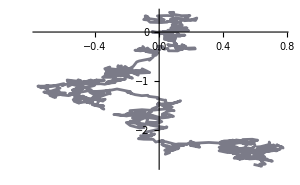

```mathematica
ListLinePlot[Transpose@sample,ColorFunction->"Rainbow",ImageSize->300]
```

Brownian increments are independent with variance ∝ Δt, so the colourful path is just one realization of an “ensemble” of such walks. This sets up why we later superpose many paths in a quantum state.

which causes to a standard behavior of a price
Do you mean “which causes a standard behavior of a price”?
Mads: yes, revised according

Here is an exponentiation of return, which causes a standard behavior of a price:

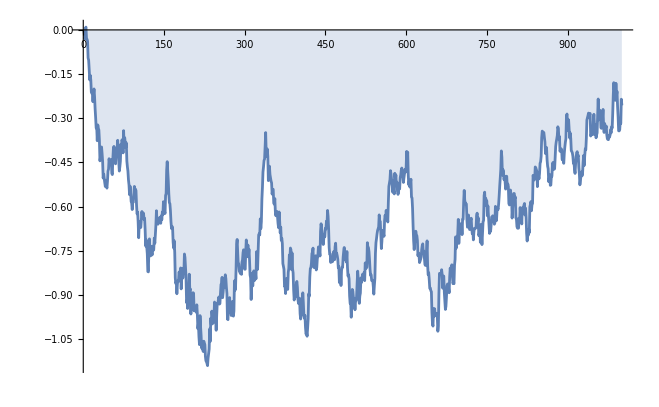

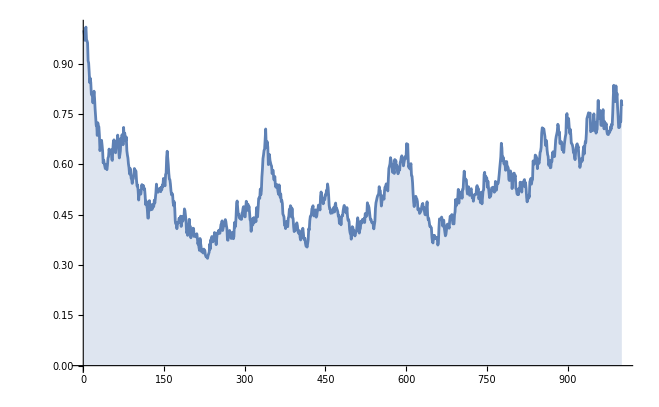

```mathematica
returns=RandomFunction[WienerProcess[],{0,1,.001},1]["States"];
price=Exp[returns];
ListLinePlot[returns,Filling->Axis]
ListLinePlot[price,Filling->Axis]
```

Exponentiating the cumulative return gives log-normal prices; notice how the drift term (μ – σ.b2/2)t tilts the trajectory upward. This is the classical analogue of the quantum return_to_price_space we code later.

We can also simply load an instance of geometric Brownian motion that also behaves like an asset price in the market:

TemporalData[…]

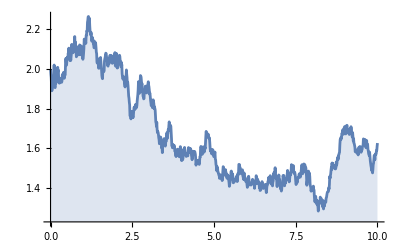

```mathematica
data=RandomFunction[GeometricBrownianMotionProcess[0,.1,2],{0,10,.01}]
ListLinePlot[data,Filling->Axis]
```

## 2. Chebyshev Polynomials in the KL Expansion

-Graphics-

Wikipedia: https://en.wikipedia.org/wiki/Chebyshev_polynomials

Article: https://arxiv.org/pdf/2402.10132.pdf

The following is an implementation of a mathematical quantum expression, as appears on p. 8 of the attached article. It is based on the Chebyshev polynomials using the recurrence relation. The KL expansion expresses () as an orthogonal sine series with i.i.d. Gaussian coefficients :

where  are Chebyshev polynomials of the second kind:

This recursive form maps neatly onto quantum add/mul blocks that Classiq already optimizes.

-Graphics-

## 3. From Formula to Quantum: Classiq Implementation Walk-Through

We will build the Brownian-motion model step by step:

1. Setup—install the classiq package and authenticate from within Mathematica.

2. Gaussian discretization—create grid points and their probabilities (we choose 2^n bins for n qubits so each probability can be amplitude-loaded exactly with prepare_state).

3. qfuncs—define the quantum function- helpers for , and , the recursive Chebyshev  and truncated Wiener series.

4. Return-to-price space—map Brownian returns to GBM prices with exponentiation.

5. Main—wrap everything up, prepare Gaussian registers, superpose time, evaluate , then convert to prices.

6. Synthesis and analyse the circuit

### Setup

If you have used only built-in Mathematica functions, you may not be used to installation of libraries. However, community members create a variety of convenient paclets, and you can run code from other programming languages written by your collaborators.

In this workshop, you will see extensive use of Classiq's library for quantum algorithms.

Note that ExternalEvaluate and related functions are unsupported in the public cloud. So you will need to download this notebook in order to use all of the features you will see in this workshop.

Installing this library can be done using the code below and takes several minutes if you don’t already have all the dependencies:

Install Wolfram Quantum Framework:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
```

PacletObject[…]

Load Wolfram Quantum Framework:

```mathematica
<<Wolfram`QuantumFramework`
<<Wolfram`QuantumFramework`QuantumOptimization`
```

Install Classiq and required dependencies:

```mathematica
classiq=ClassiqSetup[{"Session","ClassiqVersion"},"CheckDependencies"->{"pyomo","scikit-learn"},"InstallPackages"->{"scikit-learn"}]
```

Installing latest Classiq version

```mathematica
session=classiq["Session"]
```

ExternalSessionObject[…]

from classiq import *

authenticate()

### Gaussian Discretization

for having a Gaussian distribution probabilities vector?
for having the Gaussian distribution probabilities vector?
Mads: revised according

This helper is a classical pre-processing step for having a Gaussian distribution probabilities vector; only the resulting probabilities get embedded in a quantum register:

import scipy


def gaussian_discretization(num_qubits, mu=0, sigma=1, stds_around_mean_to_include=3):
    lower = mu - stds_around_mean_to_include * sigma
    upper = mu + stds_around_mean_to_include * sigma
    num_of_bins = 2**num_qubits
    sample_points = np.linspace(lower, upper, num_of_bins + 1)

    def single_gaussian(x: np.ndarray, _mu: float, _sigma: float) -> np.ndarray:
        cdf = scipy.stats.norm.cdf(x, loc=_mu, scale=_sigma)
        return cdf[1:] - cdf[0:-1]

    non_normalized_pmf = (single_gaussian(sample_points, mu, sigma),)
    real_probs = non_normalized_pmf / np.sum(non_normalized_pmf)
    return sample_points[:-1], real_probs[0].tolist()

import numpy as np

from classiq import *

PI = np.pi
L = 4
TIME_STEPS = 1
NUM_QUBITS_GAUSSIAN = 4

MU = 1
SIGMA = 2

grid_points, probabilities = gaussian_discretization(NUM_QUBITS_GAUSSIAN)

```mathematica
gridPoints=ExternalEvaluate[session,"grid_points.tolist()"]
```

{-3.,-2.625,-2.25,-1.875,-1.5,-1.125,-0.75,-0.375,0.,0.375,0.75,1.125,1.5,1.875,2.25,2.625}

```mathematica
probabilities =ExternalEvaluate[session,"probabilities"]
```

{0.00299062,0.00791339,0.0182211,0.0365094,0.0636592,0.0965936,0.127547,0.146565,0.146565,0.127547,0.0965936,0.0636592,0.0365094,0.0182211,0.00791339,0.00299062}

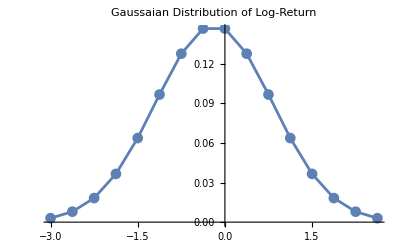

```mathematica
ListLinePlot[Transpose[{gridPoints,probabilities}],PlotLabel->"Gaussaian Distribution of Log-Return",PlotMarkers->Automatic]
```

NUM_QUBITS_GAUSSIAN = 1
grid_points, probabilities = gaussian_discretization(NUM_QUBITS_GAUSSIAN)

### Quantum Function

cos and sin function: is this one function or two?
The next sentence uses “it” - should it be “them”?
Mads: revised according

For simplicity, we will build the cos and sin functions by their Taylor approximation. Notice the definition of them in a quantum function, done using simple add/mul operations, which will be translated into quantum addition and multiplications that are applied in parallel worlds:

# Calculate sin(pi*x) and 2*cos(pi*x) using Taylor expansion


@qperm
def two_cos_pi_x(x: Const[QNum], out: Output[QNum]):
    out |= -2 * PI * (x - 0.5)  # expansion around x=0.5


@qperm
def sin_pi_x(x: Const[QNum], out: Output[QNum]):
    out |= -5 * (x - 0.5) ** 2 + 1  # expansion around x=0.5

ExternalFunction[…]

These second-order Taylor polynomials are fine for the demo:

ExternalFunction[…]

@qfunc
def main(x: Output[QNum[3, UNSIGNED, 3]], y: Output[QNum]):
    allocate(x)
    hadamard_transform(x)
    sin_pi_x(x, y)

qprog_sin = synthesize(main)
show(qprog_sin)

Quantum program link: https://platform.classiq.io/circuit/38cUQtsJYNLOiU0klzawoG7tpm1

-Graphics-

Let’s execute and see that x values are entangled with values of y that are a Taylor approximation of sin around x=0.5:

job = execute(qprog_sin)
job.open_in_ide()

```mathematica
Sin[0.75*Pi]
```

0.707107

-Graphics-

## Chebyshev Polynomials

The Chebyshev polynomials are a sequence of orthogonal polynomials that are related to de Moivre’s formula and the trigonometric functions. They are defined by the recurrence relation:

@qperm
def uk(two_x: Const[QNum], uk_1: Const[QNum], uk_2: Const[QNum], uk: Output[QNum]):
    uk |= two_x * uk_1 - uk_2


@qfunc
def main(x: Output[QNum[2, UNSIGNED, 2]]):
    allocate(x)
    hadamard_transform(x)
    U = [QNum(f"U{k}") for k in range(L)]
    U[0] |= 1
    U[1] |= 2 * x
    for k in range(2, L):
        uk(x, uk_1=U[k - 1], uk_2=U[k - 2], uk=U[k])


qprog_uk = synthesize(main)

Loop depth grows O(L), so doubling the truncation order only linearly increases the gate count—one of the reasons the KL + Chebyshev approach is hardware friendly:

show(qprog_uk)

Quantum program link: https://platform.classiq.io/circuit/38cUheEdVUHq0N06RiC6zIVwB7D

-Graphics-

## Brownian Motion

The Brownian motion is a stochastic process that models the random movement of particles in a fluid. The approximate solution in this context is the truncated Wiener series:

@qfunc
def truncated_wiener_series(t: QNum, out: Output[QNum]):
    As = [QNum(f"a{i}") for i in range(L)]
    for a in As:
        prepare_state(probabilities, 0, a)

    two_cos_pi_t = QNum("two_cos_pi_t")
    sin_pi_t = QNum("sin_pi_t")
    U = [QNum(f"U{k}") for k in range(L)]

    two_cos_pi_x(x=t, out=two_cos_pi_t)
    U[0] |= 1
    U[1] |= two_cos_pi_t
    for k in range(2, L):
        uk(two_cos_pi_t, uk_1=U[k - 1], uk_2=U[k - 2], uk=U[k])

    sin_pi_x(x=t, out=sin_pi_t)

    out |= As[0] * t + (2**0.5 / PI) * sin_pi_t * sum(
        [As[i] * U[i] for i in range(1, L)]
    )

    for a in As:
        drop(a)

    for u in U:
        drop(u)

ExternalFunction[…]

The return to price space is a mathematical operation that converts the returns of a stock to its price. It is defined as:

@qperm
def return_to_price_space(
    returns: Const[QNum], t: Const[QNum], price: Output[QNum]
) -> None:
    price |= (SIGMA * returns + (MU - SIGMA**2 / 2) * t) + 1

ExternalFunction[…]

## All Together: Main Function

@qfunc
def main(t: Output[QNum], G: Output[QNum]):
    # Allocate qubits and prepare distributions
    B = QNum("B")

    allocate(TIME_STEPS, t)
    hadamard_transform(t)

    # Create the truncated wiener series
    truncated_wiener_series(t, B)

    # Return to price space
    return_to_price_space(returns=B, t=t, price=G)

    drop(B)

ExternalFunction[…]

## Synthesize and Show the Quantum Program

qmod = create_model(
    entry_point=main,
    constraints=Constraints(optimization_parameter="width", max_width=139),
    preferences=Preferences(transpilation_option="none"),
)
qprog = synthesize(qmod)
show(qprog)

Quantum program link: https://platform.classiq.io/circuit/38cVevB3uB9IO3eBBeTAV7lLOwz

-Graphics-

-Graphics-

## Final Reflection and Quantum Roadmap

This notebook shows that a mathematically heavy model (KL-truncated geometric Brownian motion plus Chebyshev recursion) becomes circuit light once its randomness is moved into amplitudes.

Once preparing->When preparing?
Mads: revised according

When preparing this stochastic model, and in order to calculate expected payoff of an asset, we should apply the following steps:

1. Amplitude loading puts the Gaussian coefficients into superposition with  gates, matching the power-of-two grid used in the earlier cells.

2. A first layer of quantum amplitude estimation (QAE) turns the time average of the price path into a measurable amplitude; a second QAE wraps the payoff. The double nesting costs  queries but still beats classical Monte Carlo at .

3. The article hints at a shortcut—dropping one QAE by smart time subsampling—to reach  depth without extra qubits, though the hidden constants are left vague.

Overall, the notebook highlights that while the classical formulation is algebraically dense, the quantum implementation becomes quite structured. This allows finance practitioners to focus on modeling, while relying on automated synthesis tools to handle circuit-level challenges.